## Application of Flexible Numerology to Blockage Mitigation in 5G-mmWave Networks

Author : Fadhil Firyaguna
Affiliation: CONNECT Centre, Trinity College Dublin
Email: firyaguf@tcd.ie

This work has emanated from the research conducted within  the  scope  of NEMO  (Enabling  Cellular  Networks to  Exploit  Millimetre-wave  Opportunities )project  financially supported by the Science Foundation Ireland (SFI) under Grant No.  14/US/I3110  and  with  partial  support  of  the  European Regional Development Fund under Grant No. 13/RC/2077. We are  thankful  to  Danny  Finn  who  kindly  assisted  us  with  the Wolfram Mathematica software. 

This Mathematica Notebook generates the results published in the paper “Application of Flexible Numerology to Blockage Mitigation in 5G-mmWave Networks” submitted to IEEE GLOBECOM 2019.

## System Model

### System Parameters

```mathematica
txPower = 20; (*dBm*)
txPower = 10^(txPower/10); (*mW*)
noiseDensity = -174; (*dB*)
noiseDensity = 10^(noiseDensity/10);(*mW*)

environment = "carpark";(*"carpark","office","anechoic"*)

antGain = 1;
txDistance = {1,10};(*m*)
apHeight = 5;(*m*)

bodyDistance ={0.0001,0.2};(*m*)
bodyWidth = 0.4;(*m*)
bodyHeight = 0.4;(*m*)

slotTimes = {0.25,0.125,0.0625}; (*ms*)
rbBandwidth = {720,1440,2880}; (*kHz*)

frameBandwdith = Floor[100000/2880]*2880; (*kHz*)
allocWindow = {0.25,1,5}; (*ms*)
```

### Channel Characteristics

-Graphics-

```mathematica
Switch[environment,
"carpark",
(* Car Park *)
	path0LOS = -48.7; (*dBi*)
	path0LOS = 10^(path0LOS/10);
	pathExponentLOS = 1.53;
	riceK = 10^(11.9/10);
	mLOS = (riceK^2+2 riceK +1)/(2 riceK +1);
	αLOS = 10.30; (*α*)
	βLOS = 1/0.11;(*1/β*)
	path0NLOS  = -88.8; (*dBi*)
	path0NLOS = 10^(path0NLOS/10);
	pathExponentNLOS = 1.98;
	mNLOS = 2.74;
	αNLOS = 5.11;
	βNLOS = 0.23;,
"anechoic",
(* anechoic *)
	path0LOS = -43; (*dBi*)
	path0LOS = 10^(path0LOS/10);
	pathExponentLOS = 1.41;
	riceK = 10^(12.5/10);
	mLOS = (riceK^2+2 riceK +1)/(2 riceK +1);
	αLOS = 17.39; (*α*)
	βLOS = 1/0.06;(*1/β*)
	path0NLOS  = -75.5; (*dBi*)
	path0NLOS = 10^(path0NLOS/10);
	pathExponentNLOS = 1.86;
	mNLOS = 1.94;
	αNLOS = 10.27;
	βNLOS = 0.11;,
"office",
(* office *)
	path0LOS = -45.1; (*dBi*)
	path0LOS = 10^(path0LOS/10);
	pathExponentLOS = 1.18;
	riceK = 10^(5.7/10);
	mLOS = (riceK^2+2 riceK +1)/(2 riceK +1);
	αLOS = 7.01;
	βLOS = 1/0.15;
	path0NLOS  = -57.4; (*dBi*)
	path0NLOS = 10^(path0NLOS/10);
	pathExponentNLOS = 1.07;
	mNLOS = 2.35;
	αNLOS = 5.77;
	βNLOS = 0.20
];
```

### SNR on Composite Fading Channel

based on the probability of outage in equation (15) in
On the Performance Analysis of Composite Multipath/Shadowing Channels Using the G-Distribution by Laourine et al.

```mathematica
Ay[m_,ya_,α_,β_]:=(α ya)^((2m+1)/4)/Gamma[m] √((2 α β)/π)Exp[α β] (m/ya)^m;
By[ya_,α_,β_]:= β √(α/ya);
Cy[ya_,α_]:=α ya;
Dy[m_,β_]:= 2 m/β;
```

```mathematica
ccdfSNR[y_,ya_,m_,α_,β_] := Ay[m,ya,α,β]*Gamma[m]*Sum[(2^n y^(m-n))/((By[ya,α,β] Dy[m,β])^n(m-n)!) *BesselK[m-n+1/2,By[ya,α,β] * Sqrt[Cy[ya,α]+  Dy[m,β] y ]]/Sqrt[Cy[ya,α]+  Dy[m,β] y ]^(m-n+1/2),{n,0,m}];
```

### Spectral Efficiency

```mathematica
ccdfSElos[s_,d_]:=ccdfSNR[2^s-1,(txPower * antGain * path0LOS * Sqrt[d^2+apHeight^2]^-pathExponentLOS)/(frameBandwdith*10^3*noiseDensity),Ceiling[mLOS],αLOS,βLOS];
ccdfSEnlos[s_,d_]:=ccdfSNR[2^s-1,(txPower * antGain * path0NLOS * Sqrt[d^2+apHeight^2]^-pathExponentNLOS)/(frameBandwdith*10^3*noiseDensity),Ceiling[mNLOS],αNLOS,βNLOS];
```

```mathematica
expectedSElos[d_]:= NIntegrate[ccdfSElos[s,d],{s,0,40}];
expectedSEnlos[d_]:= NIntegrate[ccdfSEnlos[s,d],{s,0,40}];
```

```mathematica
avgSElos = Table[ With[ {d=d},Evaluate[ expectedSElos[d] ] ],{d,txDistance}];
avgSEnlos = Table[ With[ {d=d},Evaluate[ expectedSEnlos[d] ] ],{d,txDistance}];
```

```mathematica
Save[StringJoin[{"avgSElos_",environment}],avgSElos];
Save[StringJoin[{"avgSEnlos_",environment}],avgSEnlos];
```

### Probability of Self-blockage

```mathematica
p0[d_,bodyDistance_]:=Piecewise[{{ArcTan[bodyWidth/(2 bodyDistance)]/π,d≥ bodyDistance apHeight/bodyHeight}},
				0];
```

### Probability of LOS

```mathematica
q[d_,r0_]:= (1-p0[d,r0]);
```

### Probability of n slots transmitted in LOS

Expected number of resource blocks with duration t and bandwidth b transmitted in LOS within ta seconds and ba Hertz
ta could be the allocation scheduling window

```mathematica
probN[n_,q_,t_,ta_,mint_]:= Piecewise[{{q^(ta/mint),n==ta/t},{q^(n t/mint)(1-q), n<ta/t}}];
```

```mathematica
expectedN[q_,t_,ta_,mint_]:= Sum[n probN[n,q,t,ta,mint],{n,0,ta/t}];
```

```mathematica
evalN=Table[
With[{t=slotTimes[[ti]],
	b=rbBandwidth[[ti]],
	mint=Min[slotTimes]},
expectedN[q[d,r0],t,ta,mint] 
],
{ta,allocWindow},
{d,txDistance},
{r0,bodyDistance},
{ti,1,Length[slotTimes]}
];
```

### Aggregation Efficiency

OVERHEAD in N slots aggregation
3/(14 N) overhead

N = (allocation window)/(slot duration)
overhead = (3 t)/(14 ta)

```mathematica
aggEfficiency = Table[1-(3 t)/(14 ta),{t,slotTimes},{ta,allocWindow}];
```

### Transmission Efficiency

```mathematica
txEfficiency = With[{loss=0.05},
Table[1-loss t,{t,0,Length[slotTimes]-1}]
];
```

### Expected Data Rate

```mathematica
expectedR = Table[ 
With[{Nmax=allocWindow[[tai]]/slotTimes[[ti]]},
aggEfficiency[[ti,tai]]  txEfficiency[[ti]] (10^3 frameBandwdith)/Nmax( evalN[[tai,di,r0i,ti]] avgSElos[[di]] + (Nmax-evalN[[tai,di,r0i,ti]]) avgSEnlos[[di]])
],
{ti,1,Length[slotTimes]},
{di,1,Length[txDistance]},
{r0i,1,Length[bodyDistance]},
{tai,1,Length[allocWindow]}
];
```

```mathematica
Save[StringJoin[{"expectedR_",environment}],expectedR];
```

Before evaluating the Numerical Results section, please change the “environment” variable (in the System Parameters sub-section) from “carpark” to “office” and run this section again.

## Numerical Results

### Expected Data Rate

```mathematica
expectedRcarpark = Get["expectedR_carpark"];
expectedRoffice = Get["expectedR_office"];
```

Part::partw: Part 4 of {0.785714,0.946429,0.989286} does not exist.

Part::partw: Part 5 of {0.785714,0.946429,0.989286} does not exist.

Part::partw: Part 6 of {0.785714,0.946429,0.989286} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

### UE in Hand scenario, t_S = 1 ms

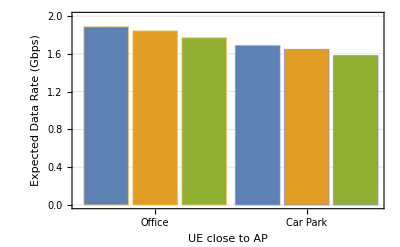
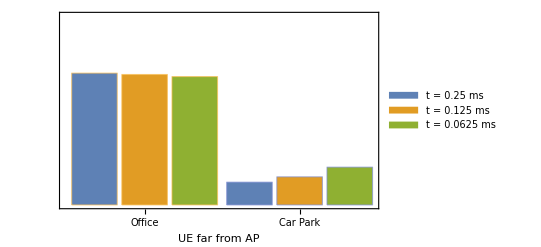

```mathematica
With[{r0i=2},
Row[{
BarChart[{
Labeled[10^-9 expectedRoffice[[All,1,r0i,2]],"Office"],
Labeled[10^-9 expectedRcarpark[[All,1,r0i,2]],"Car Park"]
},
PlotRange->{0,2},
BarSpacing->Small,
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate (Gbps)"},
FrameTicks->Automatic,
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRoffice[[All,2,r0i,2]],"Office"],
Labeled[10^-9 expectedRcarpark[[All,2,r0i,2]],"Car Park"]
},
PlotRange->{0,2},
BarSpacing->Small,
ChartStyle->{EdgeForm[Thick],ColorData[97]},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{.75,.75}],
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```

### UE in Pocket scenario, t_S = 1 ms

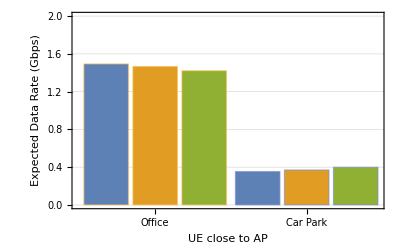
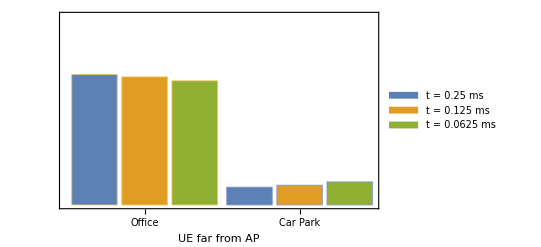

```mathematica
With[{r0i=1},
Row[{
BarChart[{
Labeled[10^-9 expectedRoffice[[All,1,r0i,2]],"Office"],
Labeled[10^-9 expectedRcarpark[[All,1,r0i,2]],"Car Park"]
},
PlotRange->{0,2},
BarSpacing->Small,
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate (Gbps)"},
FrameTicks->Automatic,
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRoffice[[All,2,r0i,2]],"Office"],
Labeled[10^-9 expectedRcarpark[[All,2,r0i,2]],"Car Park"]
},
PlotRange->{0,2},
BarSpacing->Small,
ChartStyle->{EdgeForm[Thick],ColorData[97]},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{.75,.75}],
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```

### UE in Hand scenario, Car Park environment

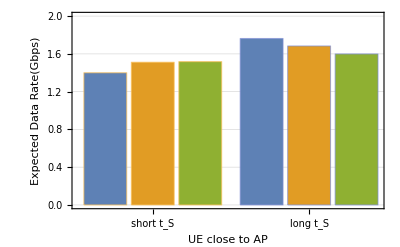
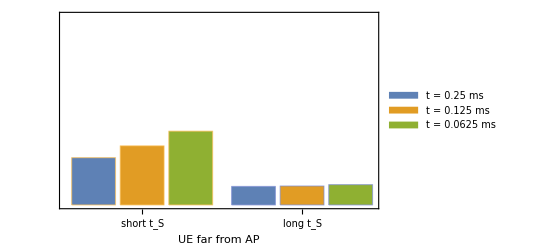

```mathematica
With[{r0i=2},
Row[{
BarChart[{
Labeled[10^-9 expectedRcarpark[[All,1,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRcarpark[[All,1,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate(Gbps)"},
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRcarpark[[All,2,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRcarpark[[All,2,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{.75,.75}],
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```

### UE in Pocket scenario, Car Park environment

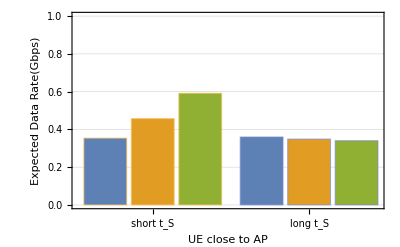
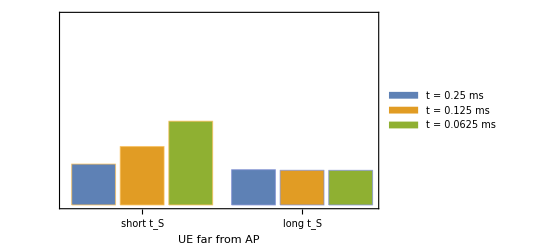

```mathematica
With[{r0i=1},
Row[{
BarChart[{
Labeled[10^-9 expectedRcarpark[[All,1,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRcarpark[[All,1,r0i,3]],"long t_S"]
},
PlotRange->{0,1},
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate(Gbps)"},
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRcarpark[[All,2,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRcarpark[[All,2,r0i,3]],"long t_S"]
},
PlotRange->{0,1},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{.75,.75}],
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```

### UE in Hand scenario, Office environment

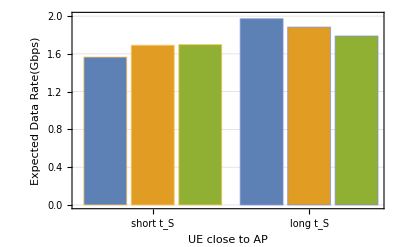
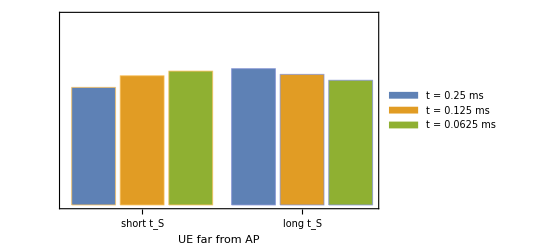

```mathematica
With[{r0i=2},
Row[{
BarChart[{
Labeled[10^-9 expectedRoffice[[All,1,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRoffice[[All,1,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate(Gbps)"},
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRoffice[[All,2,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRoffice[[All,2,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{.25,.80}],
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```

### UE in Pocket scenario, Office environment

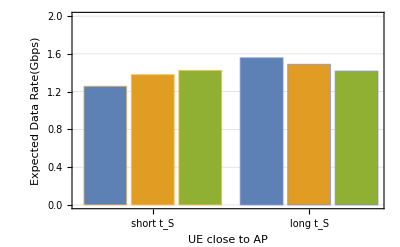
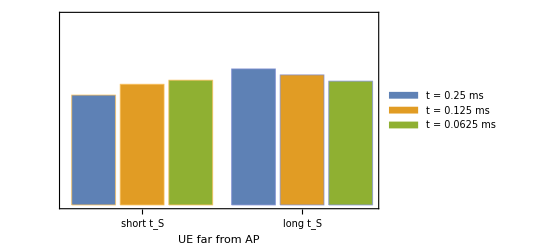

```mathematica
With[{r0i=1},
Row[{
BarChart[{
Labeled[10^-9 expectedRoffice[[All,1,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRoffice[[All,1,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE close to AP","Expected Data Rate(Gbps)"},
ImageSize->{Automatic,200}],
BarChart[{
Labeled[10^-9 expectedRoffice[[All,2,r0i,1]],"short t_S"],
Labeled[10^-9 expectedRoffice[[All,2,r0i,3]],"long t_S"]
},
PlotRange->{0,2},
ChartLegends->Placed[(Row[{"t = ",#," ms"}]&/@slotTimes),{0.25,.80}],
ChartStyle->{EdgeForm[Thick],ColorData[97]},
GridLines->Automatic ,
Frame->True,
FrameStyle->13,
FrameLabel->{"UE far from AP",None},
FrameTicks->{Automatic,None},
ImageSize->{Automatic,200}]
}]
]
```